```mathematica
Needs["Quantum`Computing`"];
SetQuantumAliases[];
```

```mathematica
M = 6;
n= 4;
```

```mathematica
Hdim=  Subscript[Tr, OverHat[1],OverHat[2],OverHat[3],OverHat[4]][Subscript[σ, 0,OverHat[1]]·Subscript[σ, 0,OverHat[2]]·Subscript[σ, 0,OverHat[3]]·Subscript[σ, 0,OverHat[4]]];
```

```mathematica
H=Sum[Subscript[σ, 𝒵,î]·Subscript[σ, 𝒵,OverHat[i+1]]+ Subscript[σ, 𝒳,î] ,{i,1,n}]
```

σ_(𝒵,OverHat[1])·σ_(𝒵,OverHat[2])+σ_(𝒵,OverHat[2])·σ_(𝒵,OverHat[3])+σ_(𝒵,OverHat[3])·σ_(𝒵,OverHat[4])+σ_(𝒵,OverHat[4])·σ_(𝒵,OverHat[5])+σ_(𝒳,OverHat[1])+σ_(𝒳,OverHat[2])+σ_(𝒳,OverHat[3])+σ_(𝒳,OverHat[4])

```mathematica
𝕆 = Subscript[σ, 0,OverHat[1]]·Subscript[σ, 𝒵,OverHat[2]]·Subscript[σ, 0,OverHat[3]]·Subscript[σ, 0,OverHat[4]];
```

```mathematica
bv = Table[0,{i,1,M}];
A = Table[0,{i,1,M}];
Kv = Table[0,{i,1,M}];
```

```mathematica
𝔏[𝔒_]:=  EvaluateCommutators[⟦H,𝔒⟧_-]
```

```mathematica
rk[A_,B_] := (Subscript[Tr, OverHat[1],OverHat[2],OverHat[3],OverHat[4]][SuperDagger[(A)]·B])/Hdim
```

```mathematica
V =FullSimplify[ 𝔏[1/2 𝔏[𝕆]] - 2 𝕆]
```

-2 (σ_(𝒵,OverHat[1])·σ_(𝒳,OverHat[2])·σ_(0,OverHat[3])+σ_(0,OverHat[1])·σ_(𝒳,OverHat[2])·σ_(𝒵,OverHat[3]))·σ_(0,OverHat[4])

```mathematica
rk[V,V]
```

8

```mathematica
bv[[2]] = √rk[𝔏[𝕆],𝔏[𝕆]]
```

2

```mathematica
Kv
```

{0,0,0,0,0,0}

```mathematica
Kv[[1]] = 𝕆
```

σ_(0,OverHat[1])·σ_(𝒵,OverHat[2])·σ_(0,OverHat[3])·σ_(0,OverHat[4])

```mathematica
A[[2]] =𝔏[ 𝕆];
bv[[2]] = √rk[A[[2]],A[[2]]];
Kv[[2]] = 1/bv[[2]] A[[2]] ;
```

```mathematica
For[i = 3,i ≤ M,i ++, 

A[[i]] =  𝔏[Kv[[i-1]]] - bv[[i-1]] Kv[[i-2]];

bv[[i]] = √rk[A[[i]],A[[i]]];

Kv[[i]] = 1/bv[[i]] A[[i]];

];
```

The bv calculation (Trace to be exact) is the bottle neck

```mathematica
bv
```

{0,2,2 √2,2 √3,√(46/3),√(1246/69)}

```mathematica
data = Table[{i-1,Log[bv[[i]]]},{i,1,Length[bv]}]
```

{{0,-∞},{1,Log[2]},{2,Log[2 √2]},{3,Log[2 √3]},{4,1/2 Log[46/3]},{5,1/2 Log[1246/69]}}

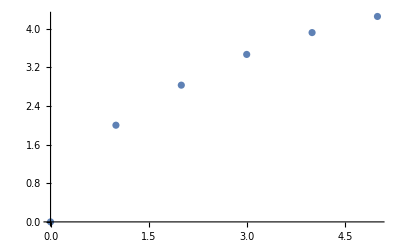

```mathematica
ListPlot[ Table[{i-1,bv[[i]]},{i,1,Length[bv]}]]
```

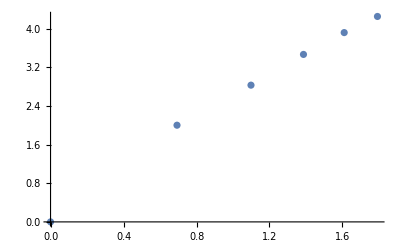

```mathematica
ListPlot[ Table[{Log[i],bv[[i]]},{i,1,Length[bv]}]]
```

```mathematica
Evaluate[Subscript[σ, 𝒵,OverHat[1]]·Subscript[σ, 𝒵,OverHat[1]]]
```

σ_(0,OverHat[1])

```mathematica
KroneckerDelta[h,j](KroneckerDelta[a,b] Subscript[σ, 0,î] + 1/2 ⟦Subscript[σ, a,ĥ],Subscript[σ, b,ĵ] ⟧_- )
```

a,b h,j σ_(0,OverHat[7])

```mathematica
⟦Subscript[σ, 𝒵,OverHat[2]]·Subscript[σ, 𝒳,OverHat[3]],Subscript[σ, 𝒳,OverHat[2]]·Subscript[σ, 𝒳,OverHat[3]] ⟧_-
```

2 ⅈ σ_(𝒴,OverHat[2])·σ_(0,OverHat[3])

```mathematica
⟦Subscript[σ, 𝒳,OverHat[3]],Subscript[σ, 𝒳,OverHat[3]] ⟧_-
```

0

```mathematica
Subscript[σ, 0,OverHat[3]]
```

```mathematica
⟦Subscript[σ, 𝒴,OverHat[3]],Subscript[σ, 0,OverHat[3]] ⟧_-
```

0

```mathematica
⟦Subscript[σ, 𝒳,OverHat[1]]·Subscript[σ, 𝒵,OverHat[2]]·Subscript[σ, 𝒳,OverHat[3]],Subscript[σ, 𝒳,OverHat[1]]·Subscript[σ, 𝒳,OverHat[2]]·Subscript[σ, 0,OverHat[3]] ⟧_-
```

2 ⅈ σ_(0,OverHat[1])·σ_(𝒴,OverHat[2])·σ_(𝒳,OverHat[3])

```mathematica
⟦Subscript[σ, 𝒳,OverHat[3]],Subscript[σ, 𝒵,OverHat[3]] ⟧_-
```

-2 ⅈ σ_(𝒴,OverHat[3])

```mathematica
⟦Subscript[σ, 𝒵,OverHat[3]],Subscript[σ, 𝒴,OverHat[3]] ⟧_-
```

-2 ⅈ σ_(𝒳,OverHat[3])

```mathematica
⟦Subscript[σ, 𝒵,OverHat[2]]·Subscript[σ, 𝒳,OverHat[3]]·Subscript[σ, 𝒴,OverHat[4]]·Subscript[σ, 𝒳,OverHat[5]]·Subscript[σ, 𝒵,OverHat[6]]·Subscript[σ, 𝒳,OverHat[7]],Subscript[σ, 𝒳,OverHat[2]]·Subscript[σ, 𝒴,OverHat[3]]·Subscript[σ, 𝒵,OverHat[4]]·Subscript[σ, 𝒴,OverHat[5]]·Subscript[σ, 𝒳,OverHat[6]]·Subscript[σ, 𝒵,OverHat[7]]⟧_-
```

0

```mathematica
⟦Subscript[σ, 𝒵,OverHat[2]],Subscript[σ, 𝒳,OverHat[2]]⟧_-
```

2 ⅈ σ_(𝒴,OverHat[2])